# A Pattern in the Primes

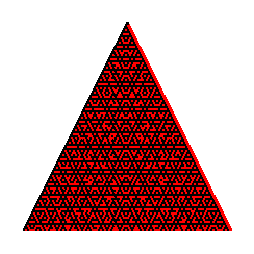
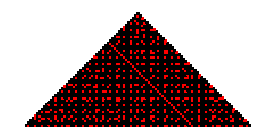
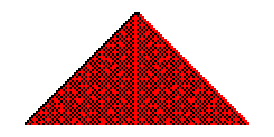

## Implementation

```mathematica
layerToTerms[n_, sides_, min_, step_] :=
With[{start = If[SameQ[min, n], 0, Last[layerToTerms[n - step, sides, min, step]]] + 1},
Range[start, start + (n * sides) - 1]]
```

```mathematica
layerToSides[n_, sides_, min_, step_] := Partition[layerToTerms[n, sides, min, step],n]
```

```mathematica
compressRows[a_, b_] := MapIndexed[Function[#1 + Part[b,First[#2 ]]], a]
```

```mathematica
isPrime[n_] := If[PrimeQ[n], 1, 0]
```

```mathematica
layerToCompressed[n_, sides_, min_, step_] := Last[FoldList[compressRows, Map[isPrime, layerToSides[n, sides, min, step], {2}]]]
```

```mathematica
generate[sides_, min_, step_] := Map[Function[layerToCompressed[#1, sides, min, step]], Range[min, sides, step]]
```

```mathematica
createRowHelper[padding_, y_, state_, rowIndex_, size_] :=
With[{x = (padding + rowIndex) * size,
        color = If[SameQ[state,0],Red, Black]}, 
{EdgeForm[Directive[Thin,White]],color, Rectangle[{x, y}, {x + size, y + size}]}]

createRow[row_, rowIndex_, maxCols_, size_] := 
 With[{padding = (maxCols  - Length[row]) / 2,
         y = (size * rowIndex)}, 
Flatten[MapIndexed[Function[createRowHelper[padding, y, #1, First[#2], size]], row ]]]
```

```mathematica
daena[sides_, size_, min_, step_] := 
With[{rows = Reverse[generate[sides, min, step]]}, 
With[{maxCols = Length[Last[rows]]},
Graphics[Flatten[MapIndexed[Function[createRow[#1, First[#2], maxCols, size]], rows]]]]]
```

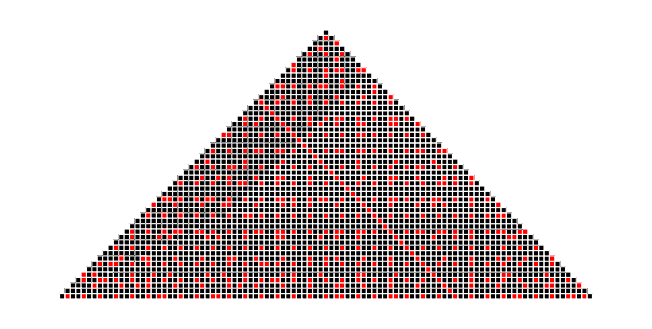

```mathematica
(*odd*)
daena[100, 5, 1, 2]
```

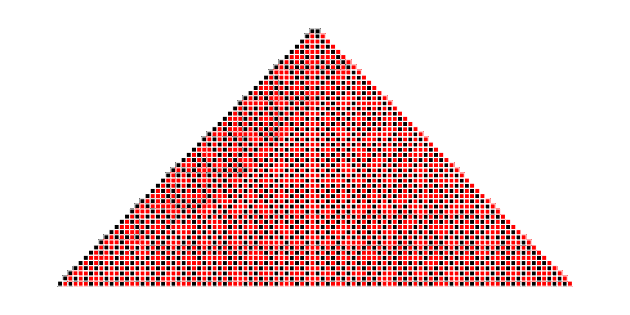

```mathematica
(*even*)
daena[100, 1, 2, 2]
```

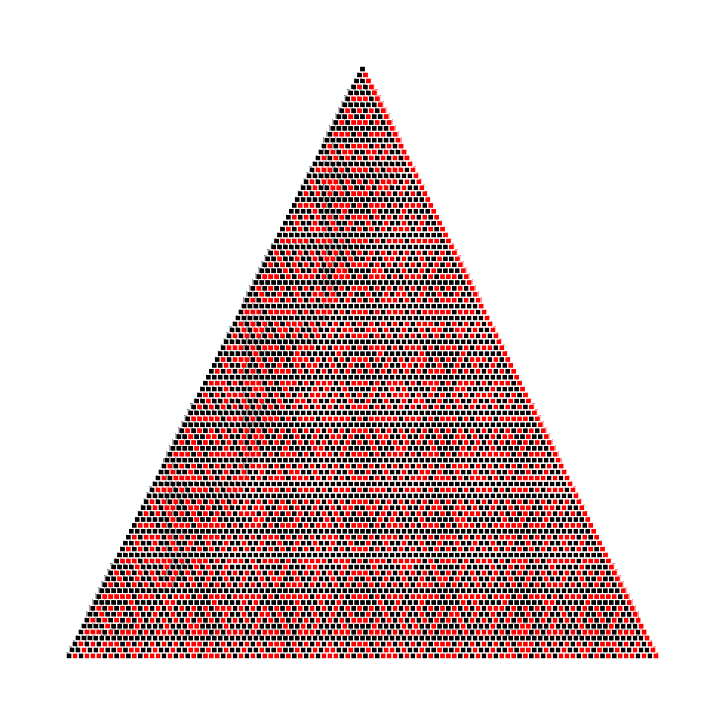

```mathematica
(*even+odd*)
daena[100, 1, 1, 1]
```